```mathematica
R=8.314;
F=83500;
```

```mathematica
CVSimulationAlpha[length_,dimension_,density_,standardVolt_,n_,T_,r_,d_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,mesh,i={},itemp,scanvolt,tempscanrate,counter=0},
mesh=Tuples[Range[length],dimension];
(distribution[#]=density)&/@mesh;
range=Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&];
Analyzer[position_]:=d*Total[Cases[distribution&/@((position+#)&/@range)-distribution[position],_Real]];
scanvolt=init;
tempscanrate=scanrate;
While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
itemp=-(standardVolt-scanvolt+8.314*T/n/F*Log[distribution[electrodeposition]])/r;
If[itemp≤0,AppendTo[i,{scanvolt,0}],
AppendTo[i,{scanvolt,itemp}];distribution[electrodeposition]-=itemp;
If[distribution[electrodeposition]<0,distribution[electrodeposition]=0];
];
distribution[#]+=Analyzer[#]&/@mesh;
];
i
];
CVSimulationAlpha[100,1,1,0.3,1,300,50,0.5,{100},0.,0.,1.5,0.001,2]
```

{{0.001,0},{0.002,0},{0.003,0},{0.004,0},{0.005,0},{0.006,0},{0.007,0},{0.008,0},{0.009,0},{0.01,0},{0.011,0},{0.012,0},{0.013,0},{0.014,0},{0.015,0},{0.016,0},{0.017,0},{0.018,0},{0.019,0},{0.02,0},{0.021,0},{0.022,0},{0.023,0},{0.024,0},{0.025,0},{0.026,0},{0.027,0},{0.028,0},{0.029,0},{0.03,0},{0.031,0},{0.032,0},{0.033,0},{0.034,0},{0.035,0},{0.036,0},{0.037,0},{0.038,0},{0.039,0},{0.04,0},{0.041,0},{0.042,0},{0.043,0},{0.044,0},{0.045,0},{0.046,0},{0.047,0},{0.048,0},{0.049,0},{0.05,0},{0.051,0},{0.052,0},{0.053,0},{0.054,0},{0.055,0},{0.056,0},{0.057,0},{0.058,0},{0.059,0},{0.06,0},{0.061,0},{0.062,0},{0.063,0},{0.064,0},{0.065,0},{0.066,0},{0.067,0},{0.068,0},{0.069,0},{0.07,0},{0.071,0},{0.072,0},{0.073,0},{0.074,0},{0.075,0},{0.076,0},{0.077,0},{0.078,0},{0.079,0},{0.08,0},{0.081,0},{0.082,0},{0.083,0},{0.084,0},{0.085,0},{0.086,0},{0.087,0},{0.088,0},{0.089,0},{0.09,0},{0.091,0},{0.092,0},{0.093,0},{0.094,0},{0.095,0},{0.096,0},{0.097,0},{0.098,0},{0.099,0},{0.1,0},{0.101,0},{0.102,0},{0.103,0},{0.104,0},{0.105,0},{0.106,0},{0.107,0},{0.108,0},{0.109,0},{0.11,0},{0.111,0},{0.112,0},{0.113,0},{0.114,0},{0.115,0},{0.116,0},{0.117,0},{0.118,0},{0.119,0},{0.12,0},{0.121,0},{0.122,0},{0.123,0},{0.124,0},{0.125,0},{0.126,0},{0.127,0},{0.128,0},{0.129,0},{0.13,0},{0.131,0},{0.132,0},{0.133,0},{0.134,0},{0.135,0},{0.136,0},{0.137,0},{0.138,0},{0.139,0},{0.14,0},{0.141,0},{0.142,0},{0.143,0},{0.144,0},{0.145,0},{0.146,0},{0.147,0},{0.148,0},{0.149,0},{0.15,0},{0.151,0},{0.152,0},{0.153,0},{0.154,0},{0.155,0},{0.156,0},{0.157,0},{0.158,0},{0.159,0},{0.16,0},{0.161,0},{0.162,0},{0.163,0},{0.164,0},{0.165,0},{0.166,0},{0.167,0},{0.168,0},{0.169,0},{0.17,0},{0.171,0},{0.172,0},{0.173,0},{0.174,0},{0.175,0},{0.176,0},{0.177,0},{0.178,0},{0.179,0},{0.18,0},{0.181,0},{0.182,0},{0.183,0},{0.184,0},{0.185,0},{0.186,0},{0.187,0},{0.188,0},{0.189,0},{0.19,0},{0.191,0},{0.192,0},{0.193,0},{0.194,0},{0.195,0},{0.196,0},{0.197,0},{0.198,0},{0.199,0},{0.2,0},{0.201,0},{0.202,0},{0.203,0},{0.204,0},{0.205,0},{0.206,0},{0.207,0},{0.208,0},{0.209,0},{0.21,0},{0.211,0},{0.212,0},{0.213,0},{0.214,0},{0.215,0},{0.216,0},{0.217,0},{0.218,0},{0.219,0},{0.22,0},{0.221,0},{0.222,0},{0.223,0},{0.224,0},{0.225,0},{0.226,0},{0.227,0},{0.228,0},{0.229,0},{0.23,0},{0.231,0},{0.232,0},{0.233,0},{0.234,0},{0.235,0},{0.236,0},{0.237,0},{0.238,0},{0.239,0},{0.24,0},{0.241,0},{0.242,0},{0.243,0},{0.244,0},{0.245,0},{0.246,0},{0.247,0},{0.248,0},{0.249,0},{0.25,0},{0.251,0},{0.252,0},{0.253,0},{0.254,0},{0.255,0},{0.256,0},{0.257,0},{0.258,0},{0.259,0},{0.26,0},{0.261,0},{0.262,0},{0.263,0},{0.264,0},{0.265,0},{0.266,0},{0.267,0},{0.268,0},{0.269,0},{0.27,0},{0.271,0},{0.272,0},{0.273,0},{0.274,0},{0.275,0},{0.276,0},{0.277,0},{0.278,0},{0.279,0},{0.28,0},{0.281,0},{0.282,0},{0.283,0},{0.284,0},{0.285,0},{0.286,0},{0.287,0},{0.288,0},{0.289,0},{0.29,0},{0.291,0},{0.292,0},{0.293,0},{0.294,0},{0.295,0},{0.296,0},{0.297,0},{0.298,0},{0.299,0},{0.3,4.44089×10^-18},{0.301,0.00002},{0.302,0.0000400119},{0.303,0.0000600359},{0.304,0.0000800717},{0.305,0.00010012},{0.306,0.000120179},{0.307,0.000140251},{0.308,0.000160335},{0.309,0.000180431},{0.31,0.000200539},{0.311,0.000220659},{0.312,0.000240791},{0.313,0.000260935},{0.314,0.000281091},{0.315,0.000301259},{0.316,0.00032144},{0.317,0.000341632},{0.318,0.000361837},{0.319,0.000382054},{0.32,0.000402283},{0.321,0.000422524},{0.322,0.000442778},{0.323,0.000463043},{0.324,0.000483321},{0.325,0.000503612},{0.326,0.000523915},{0.327,0.00054423},{0.328,0.000564557},{0.329,0.000584897},{0.33,0.00060525},{0.331,0.000625615},{0.332,0.000645992},{0.333,0.000666382},{0.334,0.000686784},{0.335,0.0007072},{0.336,0.000727627},{0.337,0.000748068},{0.338,0.000768521},{0.339,0.000788987},{0.34,0.000809465},{0.341,0.000829957},{0.342,0.000850461},{0.343,0.000870979},{0.344,0.000891509},{0.345,0.000912052},{0.346,0.000932608},{0.347,0.000953178},{0.348,0.00097376},{0.349,0.000994356},{0.35,0.00101496},{0.351,0.00103559},{0.352,0.00105622},{0.353,0.00107687},{0.354,0.00109753},{0.355,0.00111821},{0.356,0.0011389},{0.357,0.0011596},{0.358,0.00118032},{0.359,0.00120105},{0.36,0.00122179},{0.361,0.00124255},{0.362,0.00126332},{0.363,0.0012841},{0.364,0.0013049},{0.365,0.00132572},{0.366,0.00134654},{0.367,0.00136739},{0.368,0.00138824},{0.369,0.00140911},{0.37,0.00143},{0.371,0.0014509},{0.372,0.00147181},{0.373,0.00149274},{0.374,0.00151368},{0.375,0.00153464},{0.376,0.00155561},{0.377,0.0015766},{0.378,0.0015976},{0.379,0.00161862},{0.38,0.00163965},{0.381,0.0016607},{0.382,0.00168176},{0.383,0.00170284},{0.384,0.00172393},{0.385,0.00174504},{0.386,0.00176617},{0.387,0.00178731},{0.388,0.00180846},{0.389,0.00182964},{0.39,0.00185083},{0.391,0.00187203},{0.392,0.00189325},{0.393,0.00191449},{0.394,0.00193574},{0.395,0.00195702},{0.396,0.0019783},{0.397,0.00199961},{0.398,0.00202093},{0.399,0.00204227},{0.4,0.00206362},{0.401,0.002085},{0.402,0.00210639},{0.403,0.00212779},{0.404,0.00214922},{0.405,0.00217066},{0.406,0.00219212},{0.407,0.0022136},{0.408,0.0022351},{0.409,0.00225662},{0.41,0.00227815},{0.411,0.00229971},{0.412,0.00232128},{0.413,0.00234287},{0.414,0.00236448},{0.415,0.00238611},{0.416,0.00240776},{0.417,0.00242943},{0.418,0.00245111},{0.419,0.00247282},{0.42,0.00249455},{0.421,0.0025163},{0.422,0.00253807},{0.423,0.00255986},{0.424,0.00258167},{0.425,0.0026035},{0.426,0.00262535},{0.427,0.00264722},{0.428,0.00266912},{0.429,0.00269104},{0.43,0.00271298},{0.431,0.00273494},{0.432,0.00275692},{0.433,0.00277893},{0.434,0.00280096},{0.435,0.00282301},{0.436,0.00284508},{0.437,0.00286718},{0.438,0.00288931},{0.439,0.00291145},{0.44,0.00293363},{0.441,0.00295582},{0.442,0.00297804},{0.443,0.00300029},{0.444,0.00302256},{0.445,0.00304486},{0.446,0.00306718},{0.447,0.00308953},{0.448,0.0031119},{0.449,0.0031343},{0.45,0.00315673},{0.451,0.00317919},{0.452,0.00320168},{0.453,0.00322419},{0.454,0.00324673},{0.455,0.0032693},{0.456,0.0032919},{0.457,0.00331452},{0.458,0.00333718},{0.459,0.00335987},{0.46,0.00338259},{0.461,0.00340534},{0.462,0.00342812},{0.463,0.00345093},{0.464,0.00347378},{0.465,0.00349665},{0.466,0.00351956},{0.467,0.00354251},{0.468,0.00356549},{0.469,0.0035885},{0.47,0.00361155},{0.471,0.00363463},{0.472,0.00365775},{0.473,0.0036809},{0.474,0.00370409},{0.475,0.00372732},{0.476,0.00375059},{0.477,0.00377389},{0.478,0.00379724},{0.479,0.00382062},{0.48,0.00384404},{0.481,0.00386751},{0.482,0.00389102},{0.483,0.00391457},{0.484,0.00393816},{0.485,0.00396179},{0.486,0.00398547},{0.487,0.0040092},{0.488,0.00403297},{0.489,0.00405679},{0.49,0.00408065},{0.491,0.00410456},{0.492,0.00412852},{0.493,0.00415253},{0.494,0.0041766},{0.495,0.00420071},{0.496,0.00422488},{0.497,0.0042491},{0.498,0.00427337},{0.499,0.0042977},{0.5,0.00432208},{0.501,0.00434653},{0.502,0.00437103},{0.503,0.00439559},{0.504,0.00442022},{0.505,0.0044449},{0.506,0.00446965},{0.507,0.00449446},{0.508,0.00451934},{0.509,0.00454429},{0.51,0.00456931},{0.511,0.00459439},{0.512,0.00461955},{0.513,0.00464478},{0.514,0.00467009},{0.515,0.00469548},{0.516,0.00472094},{0.517,0.00474648},{0.518,0.00477211},{0.519,0.00479782},{0.52,0.00482362},{0.521,0.0048495},{0.522,0.00487548},{0.523,0.00490154},{0.524,0.00492771},{0.525,0.00495397},{0.526,0.00498033},{0.527,0.00500679},{0.528,0.00503336},{0.529,0.00506004},{0.53,0.00508683},{0.531,0.00511374},{0.532,0.00514076},{0.533,0.0051679},{0.534,0.00519517},{0.535,0.00522257},{0.536,0.0052501},{0.537,0.00527777},{0.538,0.00530557},{0.539,0.00533352},{0.54,0.00536163},{0.541,0.00538988},{0.542,0.0054183},{0.543,0.00544689},{0.544,0.00547564},{0.545,0.00550457},{0.546,0.00553369},{0.547,0.005563},{0.548,0.0055925},{0.549,0.00562221},{0.55,0.00565213},{0.551,0.00568228},{0.552,0.00571265},{0.553,0.00574327},{0.554,0.00577414},{0.555,0.00580526},{0.556,0.00583666},{0.557,0.00586835},{0.558,0.00590033},{0.559,0.00593263},{0.56,0.00596526},{0.561,0.00599823},{0.562,0.00603156},{0.563,0.00606527},{0.564,0.00609938},{0.565,0.00613392},{0.566,0.00616891},{0.567,0.00620437},{0.568,0.00624033},{0.569,0.00627683},{0.57,0.00631389},{0.571,0.00635157},{0.572,0.00638989},{0.573,0.00642891},{0.574,0.00646868},{0.575,0.00650925},{0.576,0.00655069},{0.577,0.00659308},{0.578,0.00663649},{0.579,0.00668101},{0.58,0.00672677},{0.581,0.00677387},{0.582,0.00682246},{0.583,0.00687272},{0.584,0.00692482},{0.585,0.00697902},{0.586,0.00703559},{0.587,0.00709487},{0.588,0.00715728},{0.589,0.00722335},{0.59,0.00729375},{0.591,0.00736936},{0.592,0.00745136},{0.593,0.00754136},{0.594,0.00764169},{0.595,0.00775586},{0.596,0.00788955},{0.597,0.00805281},{0.598,0.00826626},{0.599,0.00858404},{0.6,0.00926818}}

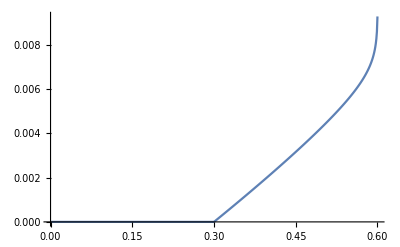

```mathematica
ListLinePlot@%
```

```mathematica
Select[Tuples[{0,1},Length[{1,1,1}]],Total[#^2]==1&]+{1,1,1}
```

{{1,1,2},{1,2,1},{2,1,1}}

```mathematica
A[1,1]
```

A[1,1]

```mathematica
Test[1,1]=1;
Cases[{Test[1,1],Test[1,2]},_Integer]
```

{1}

```mathematica
Cases[Table[a,{a,1.,3.}],_Real]
```

{1.,2.,3.}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
(fuck[#]=0.5)&/@Tuples[Range[5],3];
fuck[{1,2,3}]
```

0.5

```mathematica
fuck[#]=0.5&/@Tuples[Range[5],3]
```

```mathematica
Tuples[Range[5],1]
```

{{1},{2},{3},{4},{5}}